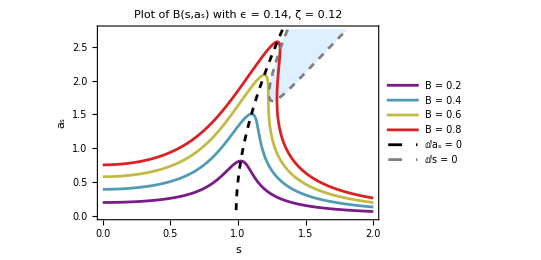

```mathematica
Clear["Global`*"](*Duffing系统固有频率附近驱动 ϵ>0*)
B[s_,A_]:=A √((1-s^2+(3ϵ)/4 A^2)^2+(2ζ s)^2);
ϵ=0.14;ζ=0.12;
f1[s_,A_]:=ϵ A^2-8/9(s+1)(s-1+1/2 √((s-1)^2-12 ζ^2(s/(s+1))^2));
f2[s_,A_]:=ϵ A^2-8/9(s+1)(s-1-1/2 √((s-1)^2-12 ζ^2(s/(s+1))^2));
f[s_,A_]:=ϵ^2 A^4-16/9(s^2-1)ϵ A^2+16/27((s^2-1)^2+4 ζ^2 s^2);
g[s_,A_]:=ϵ A^2-4/3(2 ζ^2+s^2-1);
mvals=Range[0.2,0.8,0.2];           
xmin=0;xmax=2;ymin=0;ymax=2.75;
colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[mvals]-1];
reg=RegionPlot[f[x,y]<0,{x,xmin,xmax},{y,ymin,ymax},PlotStyle->LightBlue,BoundaryStyle->None,PlotPoints->100,MaxRecursion->4];
styles=Join[colors,{Directive[Black,Dashed]},{Directive[Gray,Dashed]}];
labels=Join[Table[Style["B = "<>ToString[m],FontFamily->"Times New Roman",10],{m,mvals}],{Style["ⅆa_s = 0",FontFamily->"Times New Roman",10]},{Style["ⅆs = 0",FontFamily->"Times New Roman",10]}];
eqs=Join[Table[B[x,y]-m==0,{m,mvals}],{g[x,y]==0},{f[x,y]==0}];
con=ContourPlot[Evaluate@eqs,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->styles,PlotLegends->Placed[LineLegend[labels],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},PlotPoints->100,MaxRecursion->4];
Show[reg,con,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PerformanceGoal->"Quality",PlotLabel->"Plot of B(s,a_s) with ϵ = 0.14, ζ = 0.12",FrameLabel->{"s","a_s"}]
```

3.01402

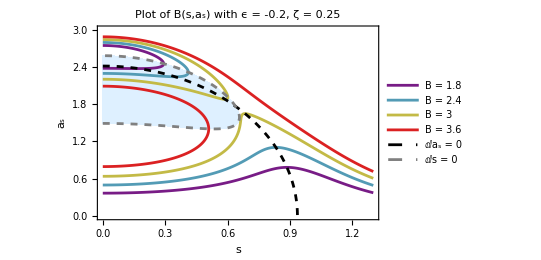

```mathematica
Clear["Global`*"](*Duffing系统固有频率附近驱动 ϵ<0*)
B[s_,A_]:=A/Abs[ϵ] √((1-s^2+(3ϵ)/4 A^2)^2+(2ζ s)^2);
ϵ=-0.2;ζ=0.25;
f1[s_,A_]:=ϵ A^2-8/9(s+1)(s-1+1/2 √((s-1)^2-12 ζ^2(s/(s+1))^2));
f2[s_,A_]:=ϵ A^2-8/9(s+1)(s-1-1/2 √((s-1)^2-12 ζ^2(s/(s+1))^2));
f[s_,A_]:=ϵ^2 A^4-16/9(s^2-1)ϵ A^2+16/27((s^2-1)^2+4 ζ^2 s^2);
g[s_,A_]:=ϵ A^2-4/3(2 ζ^2+s^2-1);
(16 √(3 √3))/9 √(ζ^3/Abs[ϵ]^3(√(1+3 ζ^2)+Sign[ϵ] √3 ζ)^3)
mvals=Range[1.8,3.6,0.6];           
xmin=0;xmax=1.3;ymin=0;ymax=3;
colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[mvals]-1];
reg=RegionPlot[f[x,y]<0,{x,xmin,xmax},{y,ymin,ymax},PlotStyle->LightBlue,BoundaryStyle->None,PlotPoints->100,MaxRecursion->4];
styles=Join[colors,{Directive[Black,Dashed]},{Directive[Gray,Dashed]}];
(*把数格式化成字符串：整数->"3"，否则保留 2 位小数*)(*把数格式化成字符串：整数->"3"，否则保留 2 位小数*)formatB[m_?NumericQ]:=If[Chop[m-Round[m]]==0,ToString[Round[m]],(*例如 3.->"3"*)ToString[m](*例如 2.75->"2.75"*)];

labels=Join[Table[Style[Row[{"B = ",formatB[m]}],(*这里用 Row 而不是直接字符串*)FontFamily->"Times New Roman",10],{m,mvals}],{Style["ⅆ\!\(\*SubscriptBox[\(a\), \(s\)]\) = 0",FontFamily->"Times New Roman",10]},{Style["ⅆs = 0",FontFamily->"Times New Roman",10]}];
eqs=Join[Table[B[x,y]-m==0,{m,mvals}],{g[x,y]==0},{f[x,y]==0}];
con=ContourPlot[Evaluate@eqs,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->styles,PlotLegends->Placed[LineLegend[labels],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},PlotPoints->100,MaxRecursion->4];
Show[reg,con,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PerformanceGoal->"Quality",PlotLabel->"Plot of B(s,a_s) with ϵ = -0.2, ζ = 0.25",FrameLabel->{"s","a_s"}]
```

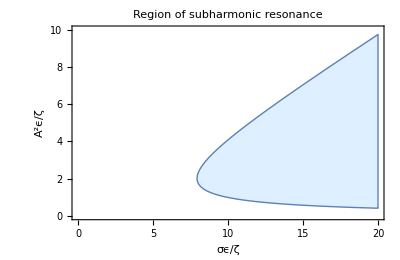

```mathematica
Clear[x,y];(*达芬系统亚谐波共振*)
RegionPlot[x>=(27/16) y&&(1/8) y (x-(63/32) y)>=1,{x,0,20},{y,0,10},PlotStyle->LightBlue,BoundaryStyle->Thick,FrameLabel->{"σϵ/ζ","A^2ϵ/ζ"},PlotPoints->60,Mesh->None,AspectRatio->0.65,PlotLabel->"Region of subharmonic resonance",BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

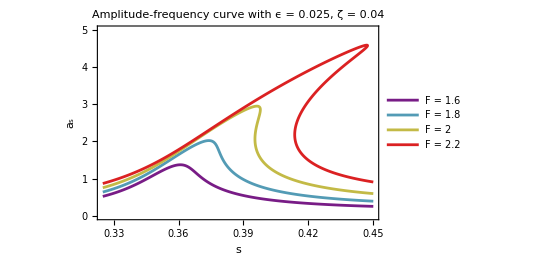

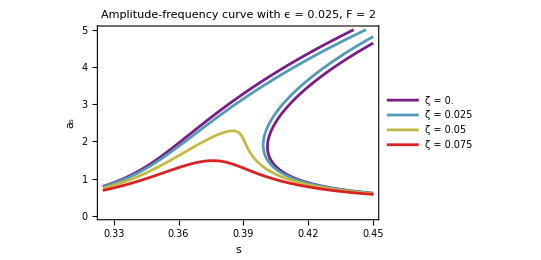

```mathematica
Clear["Global`*"](*达芬系统超谐波共振 ϵ>0*)
ϵ=0.025;
f[F_,s_,a_,ζ_]:=(ζ/ϵ)^2+((3s-1)/ϵ-3/8 a^2-3/4 F^2/((1-s^2)^2))^2-F^6/(8 a^2(1-s^2)^6);
mvals=Range[1.6,2.2,0.2];mvals2=Range[0,0.075,0.025];xmin=0.325;xmax=0.45;ymin=0;ymax=5;
colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[mvals]-1];
styles=colors;
formatF[m_?NumericQ]:=If[Chop[m-Round[m]]==0,ToString[Round[m]],(*例如 3.->"3"*)ToString[m](*例如 2.75->"2.75"*)]
labels=Table[Style["F = "<>formatF[m],FontFamily->"Times New Roman",10],{m,mvals}];
eqs=Table[f[m,x,y,0.04]==0,{m,mvals}];
labels2=Table[Style["ζ = "<>ToString[m],FontFamily->"Times New Roman",10],{m,mvals2}];
eqs2=Table[f[2,x,y,m]==0,{m,mvals2}];
ContourPlot[Evaluate@eqs,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->styles,PlotLabel->"Amplitude-frequency curve with ϵ = 0.025, ζ = 0.04",FrameLabel->{"s","a_s"},PlotLegends->Placed[LineLegend[labels],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PlotPoints->100,MaxRecursion->4,PerformanceGoal->"Quality"]
ContourPlot[Evaluate@eqs2,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->styles,PlotLabel->"Amplitude-frequency curve with ϵ = 0.025, F = 2",FrameLabel->{"s","a_s"},PlotLegends->Placed[LineLegend[labels2],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PlotPoints->100,MaxRecursion->4,PerformanceGoal->"Quality"]
```

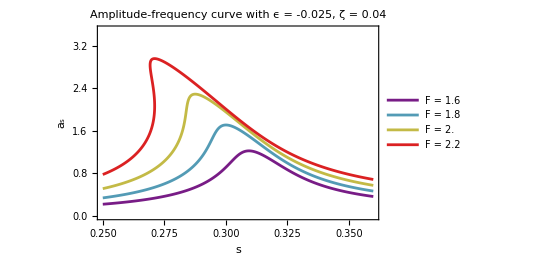

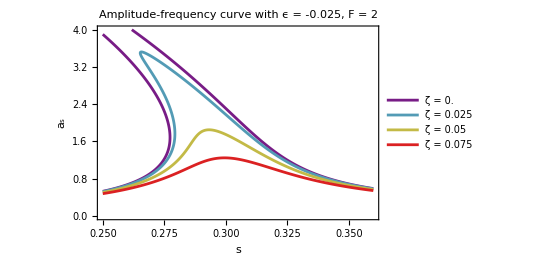

```mathematica
Clear["Global`*"](*达芬系统超谐波共振 ϵ<0*)
ϵ=-0.025;
f[F_,s_,a_,ζ_]:=(ζ/ϵ)^2+((3s-1)/ϵ-3/8 a^2-3/4 F^2/((1-s^2)^2))^2-F^6/(8 a^2(1-s^2)^6);
mvals=Range[1.6,2.2,0.2];mvals2=Range[0,0.075,0.025];xmin=0.25;xmax=0.36;ymin=0;ymax=5;
colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[mvals]-1];
styles=colors;
labels=Table[Style["F = "<>ToString[m],FontFamily->"Times New Roman",10],{m,mvals}];
eqs=Table[f[m,x,y,0.04]==0,{m,mvals}];
labels2=Table[Style["ζ = "<>ToString[m],FontFamily->"Times New Roman",10],{m,mvals2}];
eqs2=Table[f[2,x,y,m]==0,{m,mvals2}];
ContourPlot[Evaluate@eqs,{x,xmin,xmax},{y,ymin,3.5},ContourStyle->styles,PlotLabel->"Amplitude-frequency curve with ϵ = -0.025, ζ = 0.04",FrameLabel->{"s","a_s"},PlotLegends->Placed[LineLegend[labels],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PlotPoints->100,MaxRecursion->4,PerformanceGoal->"Quality"]
ContourPlot[Evaluate@eqs2,{x,xmin,xmax},{y,ymin,4},ContourStyle->styles,PlotLabel->"Amplitude-frequency curve with ϵ = -0.025, F = 2",FrameLabel->{"s","a_s"},PlotLegends->Placed[LineLegend[labels2],Right],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65,PlotPoints->100,MaxRecursion->4,PerformanceGoal->"Quality"]
```

```mathematica
Clear["Global`*"](*Mathieu方程稳定参数区域图*)
λmin=-2;λmax=34;
qmin=0;qmax=17.5;  
unstableRegion=RegionPlot[Im[N[MathieuCharacteristicExponent[λ,q]]]!=0,{λ,λmin,λmax},{q,qmin,qmax},PlotPoints->120,MaxRecursion->3,BoundaryStyle->None,PlotStyle->{HatchFilling[45 Degree,4],EdgeForm[]}];
nMax=6;  

curveA[n_,q_]:=MathieuCharacteristicA[n,q]; 
curveB[n_,q_]:=MathieuCharacteristicB[n,q];  
tongueCurves=Flatten@Table[With[{col=Black},If[n==0,{ParametricPlot[{curveA[0,q],q},{q,qmin,qmax},PlotRange->{{λmin,λmax},{qmin,qmax}},PlotStyle->{Thick,col}],ParametricPlot[{curveB[1,q],q},{q,qmin,qmax},PlotRange->{{λmin,λmax},{qmin,qmax}},PlotStyle->{Thick,col}]},{ParametricPlot[{curveA[n,q],q},{q,qmin,qmax},PlotRange->{{λmin,λmax},{qmin,qmax}},PlotStyle->{Thick,col}],ParametricPlot[{curveB[n,q],q},{q,qmin,qmax},PlotRange->{{λmin,λmax},{qmin,qmax}},PlotStyle->{Thick,col}]}]],{n,0,nMax}];
Show[unstableRegion,Sequence@@tongueCurves,Frame->True,Axes->False,FrameTicks->{Range[λmin,λmax,2],Range[qmin,qmax,2]},FrameLabel->(Style[#,14]&/@{"λ","q"}),PlotLabel->"Mathieu方程稳定性图",ImageSize->600,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AspectRatio->0.65]
```

-Graphics-